```mathematica
f[x_]= Piecewise[{{1, 0<x<1}}]
```

Piecewise[{{1, 0<x<1}, {0, True}}]

```mathematica
f1[w_]:= 1/(√(2*π))∫_(-∞)^∞ f[x]*ⅇ^(-ⅈ*w*x)ⅆx
```

```mathematica
f1[w]
```

(-ⅈ+ⅈ Cos[w]+Sin[w])/(√(2 π) w)

```mathematica
f2= 1/(√(2*π))∫_-20^20 f1[w]*ⅇ^(ⅈ*w*x)ⅆw
```

-1/(4 π)ⅈ (2 ExpIntegralEi[-20 ⅈ (-1+x)]-2 ExpIntegralEi[20 ⅈ (-1+x)]-2 ExpIntegralEi[-20 ⅈ x]+2 ExpIntegralEi[20 ⅈ x]-Log[-ⅈ/(-1+x)]+Log[ⅈ/(-1+x)]-Log[-ⅈ (-1+x)]+Log[ⅈ (-1+x)]+Log[-ⅈ/x]-Log[ⅈ/x]+Log[-ⅈ x]-Log[ⅈ x])

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

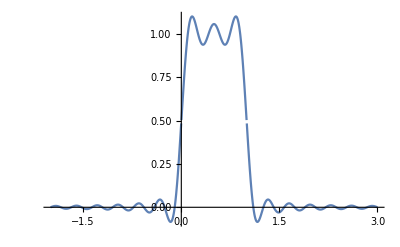

```mathematica
Plot[Re[f2],{x,-2,3}]
```

```mathematica
g[x_]:= Piecewise[{{1-x^2,-1<x<1}}]
```

```mathematica
f11[w_]:= 1/(√(2*π))∫_(-∞)^∞ g[x]*ⅇ^(-ⅈ*w*x)ⅆx
```

```mathematica
f11[w]
```

-(2 √(2/π) (w Cos[w]-Sin[w]))/w^3

```mathematica
f22= 1/(√(2*π))∫_-20^20 ⅈ*w*f11[w]*ⅇ^(ⅈ*w*x)ⅆw
```

-1/(20 π)ⅈ (ⅈ ⅇ^(-20 ⅈ (-1+x))+ⅈ ⅇ^(20 ⅈ (-1+x))-ⅈ ⅇ^(-20 ⅈ (1+x))-ⅈ ⅇ^(20 ⅈ (1+x))-20 x ExpIntegralEi[-20 ⅈ (-1+x)]+20 x ExpIntegralEi[20 ⅈ (-1+x)]+20 x ExpIntegralEi[-20 ⅈ (1+x)]-20 x ExpIntegralEi[20 ⅈ (1+x)]+10 x Log[-ⅈ/(-1+x)]-10 x Log[ⅈ/(-1+x)]+10 x Log[-ⅈ (-1+x)]-10 x Log[ⅈ (-1+x)]-10 x Log[-ⅈ/(1+x)]+10 x Log[ⅈ/(1+x)]-10 x Log[-ⅈ (1+x)]+10 x Log[ⅈ (1+x)])

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

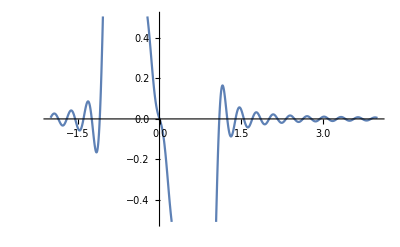

```mathematica
Plot[Re[f22], {x,-2,4}]
```

```mathematica
f111[w_]:= 1/(√(2*π))∫_(-∞)^∞ (ⅇ^(-x^2))/-2*ⅇ^(-ⅈ*w*x)ⅆx
```

```mathematica
f111[w]
```

-(ⅇ^(-w^2/4))/(2 √2)

```mathematica
f112[w_]:= 1/(√(2*π))∫_(-∞)^∞ x*ⅇ^(-x^2)*ⅇ^(-ⅈ*w*x)ⅆx
```

```mathematica
f112[w]
```

-(ⅈ ⅇ^(-w^2/4) w)/(2 √2)

```mathematica
b=1/(√(2*π))∫_-20^20 (f111[w])*ⅇ^(ⅈ*w*x)ⅆw
```

-1/4 ⅇ^(-x^2) (Erf[10-ⅈ x]+Erf[10+ⅈ x])

```mathematica
a=1/(√(2*π))∫_-20^20 (f111[w])*ⅈ*w*ⅇ^(ⅈ*w*x)ⅆw
```

(ⅇ^(-100-x (20 ⅈ+x)) (ⅈ ⅇ^(x^2) (-1+ⅇ^(40 ⅈ x))+ⅇ^(100+20 ⅈ x) √π x (Erf[10-ⅈ x]+Erf[10+ⅈ x])))/(2 √π)

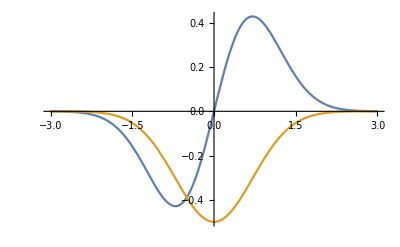

```mathematica
Plot[{a,b},{x,-3,3}]
```